# Female Satisfaction - Male Muscularity

https://twitter.com/datepsych/status/1741677937038913931 
The question is, how high is the sample count? This notebook is unfair BECAUSE I am assuming based on the sparseness of the dots, I assume each dot is one sample even though this is unlikely.
Also p-values seem to be totally useless. You run a Monte Carlo simulation, you can get any p-value you want!

-Graphics-

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done. Time to multiply the sample count by 100.

```mathematica
Y={200,200,500, 800, 900, 400, 200}
```

{200,200,500,800,900,400,200}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

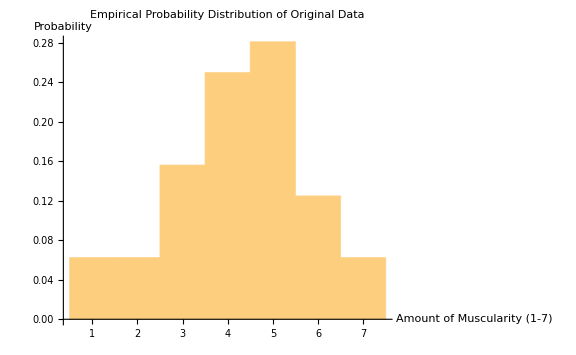

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.77691,-0.272711}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.272711}

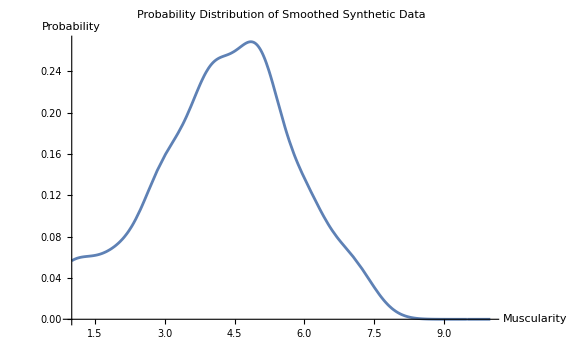

```mathematica
Plot[PDF[dist2,x],{x,1,10},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity","Probability"},ImageSize->Large]
```

Muscularity of individuals apparently follow a normal distribution

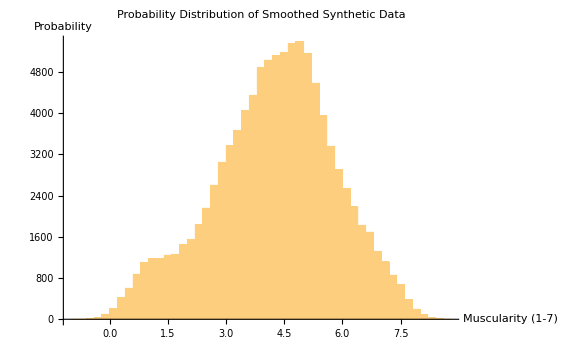

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity (1-7)","Probability"},ImageSize->Large]
```

### Testing with No Noise

We find the gradient of a line.

```mathematica
(37-30)/7
```

1

From the picture of the graph, we derive this linear fit.

```mathematica
f=a*x+b/.{a->1,b->30};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[30.+1. x]

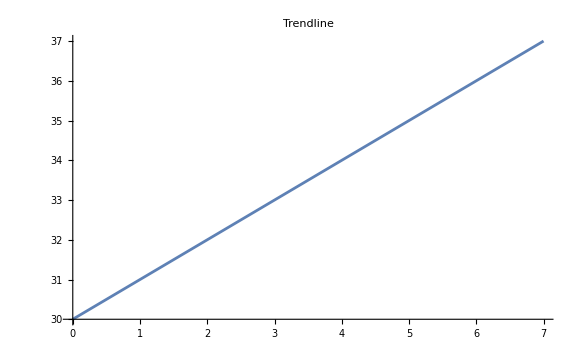

```mathematica
Plot[lm[x],{x,0,7},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

3200

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the p-value as usual, run about the model 10^4 times so as to get a distribution of possible p-values. This is the Monte Carlo simulation for possible p-value given a particular noise and eats up a lot of time. I have calibrate the noise so as to get the supposed p-value. Note that the noise to get the p-value is ridiculously high.

```mathematica
res=Table[lm=LinearModelFit[reg1[23.5],{1,x},x];lm["ParameterPValues"][[2]],{z,1,10^3}];
```

Get the assumed p-value distribution and parameters. The p-value is way too high.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.0107376,0.0389704,7.02115,65.0238}

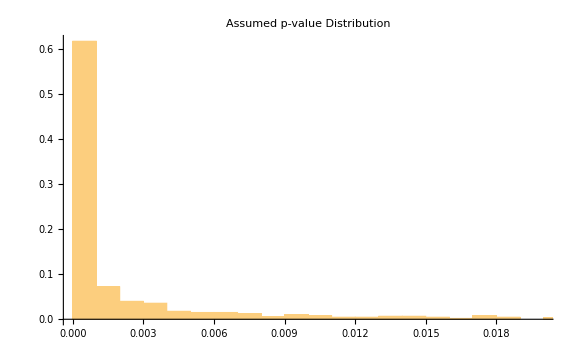

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed p-value Distribution",ImageSize->Large]
```

Replicate the graph. From the empirical distribution. Note that I am being generous by assuming they had 3200 samples. Note that this is absolutely ridiculous, so the sample size is clearly must less than 3200. Note that to achieve this p-value, you basically have to far exceed the scale of the study in the first place as part of the empirical distribution.

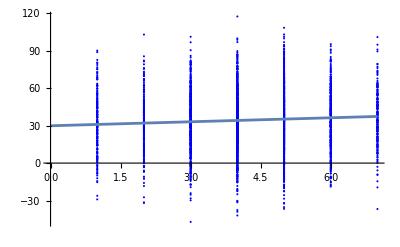

```mathematica
Show[ListPlot[reg1[23.5],PlotStyle->Blue],Plot[lm[x],{x,0,7}]]
```

### Replicating Their Linear Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times. We use purely the linear term.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[23.5],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{1.00011,0.279978,0.0674603,3.1618}

Plot the histogram of the assumed quadratic coefficient.

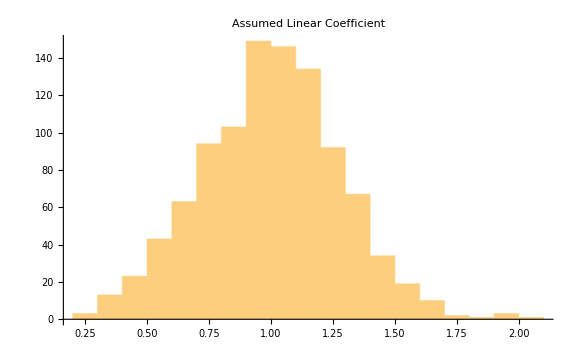

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Linear Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

This is where you get caught out. If you have a low sample count, you should get basically nothing or no correlation. How is it possible that with such a low sample count they got such a distribution?

```mathematica
ta:=RandomVariate[dist2,Length[f1]]
```

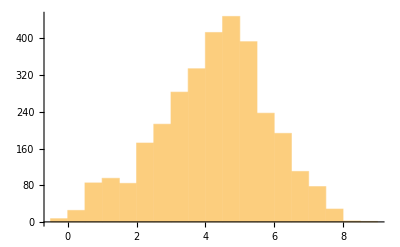

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[23.5],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{0.0039065,0.260936,2.87089}

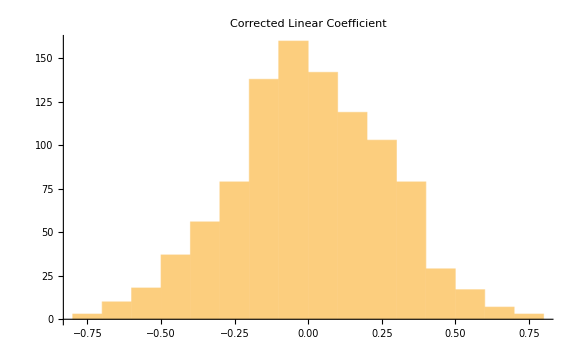

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```

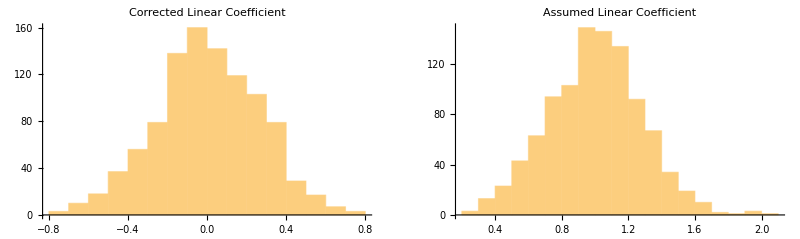

```mathematica
GraphicsGrid[{{pl2,pl1}}]
```

## Trying with low sample size.

https://twitter.com/datepsych/status/1741677937038913931 
The question is, how high is the sample count? This notebook is unfair BECAUSE I am assuming based on the sparseness of the dots, I assume each dot is one sample even though this is unlikely.
Also p-values seem to be totally useless. You run a Monte Carlo simulation, you can get any p-value you want!

-Graphics-

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done.

```mathematica
Y={2,2,5, 8, 9, 4, 2}
```

{2,2,5,8,9,4,2}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

-Graphics-

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.8088,-0.242821}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.242821}

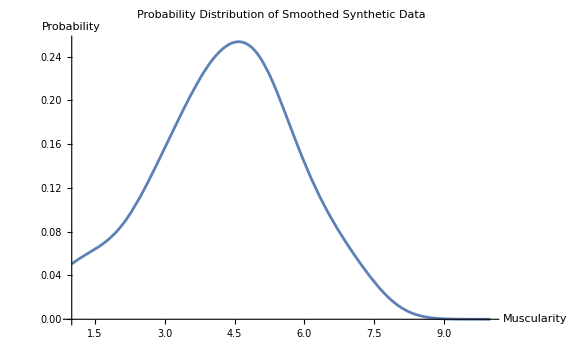

```mathematica
Plot[PDF[dist2,x],{x,1,10},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity","Probability"},ImageSize->Large]
```

Muscularity of individuals apparently follow a normal distribution

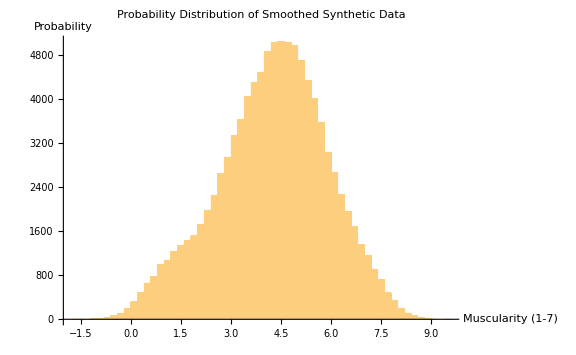

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Muscularity (1-7)","Probability"},ImageSize->Large]
```

### Testing with No Noise

We find the gradient of a line.

```mathematica
(37-30)/7
```

1

From the picture of the graph, we derive this linear fit.

```mathematica
f=a*x+b/.{a->1,b->30};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[30.+1. x]

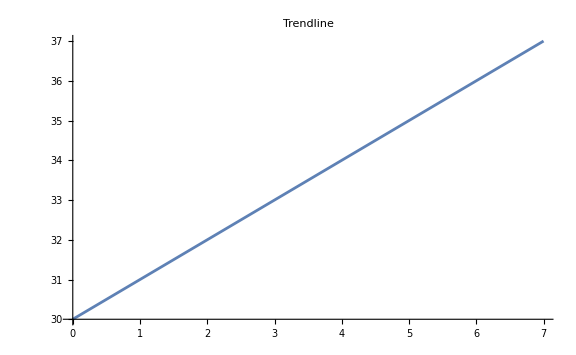

```mathematica
Plot[lm[x],{x,0,7},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

32

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the p-value as usual, run about the model 10^4 times so as to get a distribution of possible p-values. This is the Monte Carlo simulation for possible p-value given a particular noise and eats up a lot of time. I have calibrate the noise so as to get the supposed p-value.

```mathematica
res=Table[lm=LinearModelFit[reg1[2.225],{1,x},x];lm["ParameterPValues"][[2]],{z,1,10^3}];
```

Get the assumed p-value distribution and parameters.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.00780438,0.0265719,6.98769,63.0429}

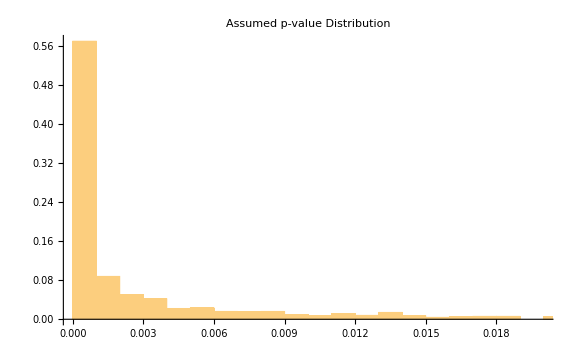

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed p-value Distribution",ImageSize->Large]
```

Replicate the graph. From the empirical distribution. I now use 32 samples from the dots they had.

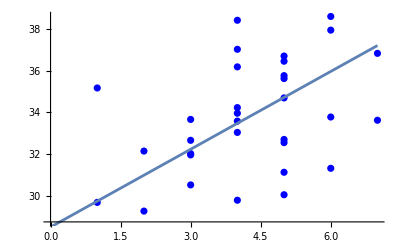

```mathematica
Show[ListPlot[reg1[2.225],PlotStyle->Blue],Plot[lm[x],{x,0,7}]]
```

### Replicating Their Linear Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times. We use purely the linear term.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[2.225],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{1.01781,0.265514,0.00216126,2.90445}

Plot the histogram of the assumed quadratic coefficient.

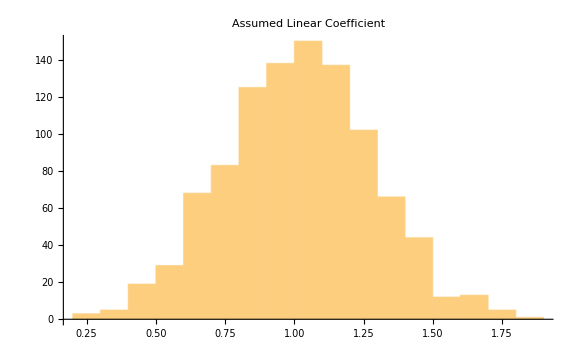

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Linear Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

This is where you get caught out. If you have a low sample count, you should get basically nothing or no correlation. How is it possible that with such a low sample count they got such a distribution?

```mathematica
ta:=RandomVariate[dist2,Length[f1]]
```

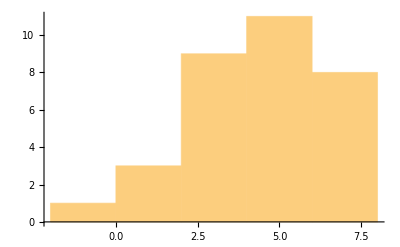

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[2.225],{1,x},x];lm2[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{0.00256046,0.30777,2.98296}

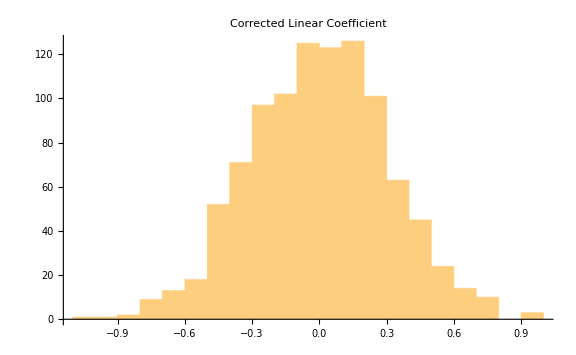

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```

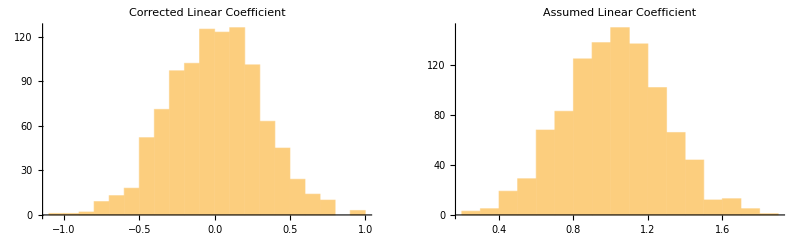

```mathematica
GraphicsGrid[{{pl2,pl1}}]
```